```mathematica
ClearAll["`*"]
$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`100."&);
```

## DKB : Initial Formulas

```mathematica
order = 3;
kmin = 0.1; R = 10; Z=2; c = 137.0359895; k =-1;
nnode = 12;
knot = Flatten[{
Table[0, {i, 1,order+1}],
Table[ kmin(R/kmin)^((i-1)/(nnode-2*4)), {i,1, nnode-2*4}],
Table[R, {i, 1,order+1}]}]
n = Length[knot]-order-2
nrem = 1;
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
```

{0,0,0,0,0.1,0.31622776601683793319988935444327185337195551393252168268575048527925944386392382213442481083793003,1.,3.1622776601683793319988935444327185337195551393252168268575048527925944386392382213442481083793003,10,10,10,10}

7

### Matrice S

```mathematica
Smat =Evaluate[Table[∫_0^R ϕi[r, ai]ϕi[r, aj]ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Smat // Dimensions, SymmetricMatrixQ[Smat]}
Smat // MatrixForm // ScientificForm
```

{{6,6},True}

(3.848429195385804464741260685538636741509643843883527135894399859029314832893758005082415127804418997×10^-2 | 2.824697038866049177255832673248901628817124022121605956882061301878215001944240814480649347382473048×10^-2 | 2.882976558077180998773080572884580093415188566821411673710688440733130076354428123868912969163005964×10^-3 | 1.225017225735702351356454052916463218582060168277099575839477834611587209192702325417989204170966035×10^-5 | 0 | 0
2.824697038866049177255832673248901628817124022121605956882061301878215001944240814480649347382473048×10^-2 | 1.256433704947498974611523234849327731797644409508525100051397600689649459932293745824674645965643991×10^-1 | 8.74782667741887005406265516805242144610423188868746171743733829507753304999901524642612990228249412×10^-2 | 7.32710403919684212091433819588135212892985038157072884555817711311454584886335706041711177838250808×10^-3 | 4.304271784739395769178334101885541716747989362760017193240408897186283933388592619541228272928745831×10^-5 | 0
2.882976558077180998773080572884580093415188566821411673710688440733130076354428123868912969163005964×10^-3 | 8.74782667741887005406265516805242144610423188868746171743733829507753304999901524642612990228249412×10^-2 | 4.042853638675203509352060727478496011982045076549739634582425569762106692236359901420720971097354735×10^-1 | 2.718371323240572723090268942819778404163284799624837430727534356038870020901779981980815482748691712×10^-1 | 2.358483540015209740523923379624191289014575443710259089204585177473199118185562441513700289983134050×10^-2 | 4.782524205265995299087037890983935240831099291955574659156009885762537703765102910601364747698606479×10^-4
1.225017225735702351356454052916463218582060168277099575839477834611587209192702325417989204170966035×10^-5 | 7.32710403919684212091433819588135212892985038157072884555817711311454584886335706041711177838250808×10^-3 | 2.718371323240572723090268942819778404163284799624837430727534356038870020901779981980815482748691712×10^-1 | 1.260865799312384545561037915480170449287248532160754447545258829370435340950577160171641554223603303 | 6.91183772050877184419528461784226838196966227948542055076334663052242567868744067570854303957656907×10^-1 | 2.175728572918148994925936455129241448512435053597611602889451516922673034421143883772672375065916242×10^-1
0 | 4.304271784739395769178334101885541716747989362760017193240408897186283933388592619541228272928745831×10^-5 | 2.358483540015209740523923379624191289014575443710259089204585177473199118185562441513700289983134050×10^-2 | 6.91183772050877184419528461784226838196966227948542055076334663052242567868744067570854303957656907×10^-1 | 9.15618628124724909410205491245202669635319458903385515560703171144688930025225246498425243482110375×10^-1 | 6.22265346345785317850514011569038873205925785443263204279152693151258473458303088006564932849159106×10^-1
0 | 0 | 4.782524205265995299087037890983935240831099291955574659156009885762537703765102910601364747698606479×10^-4 | 2.175728572918148994925936455129241448512435053597611602889451516922673034421143883772672375065916242×10^-1 | 6.22265346345785317850514011569038873205925785443263204279152693151258473458303088006564932849159106×10^-1 | 8.71518954768586481428527521604472957687283934100207016938789875110817239628541199259692385253146837×10^-1)

### Matrice ϕ

```mathematica
ϕmat =Evaluate[Table[∫_0^R ϕi[r, ai] Z/r ϕi[r, aj]ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{ϕmat // Dimensions, SymmetricMatrixQ[ϕmat]}
ϕmat // MatrixForm // ScientificForm
```

{{6,6},True}

(1.554311855395569635724044428605100506020851024345479786573044223196615007996995963650904321003232344 | 6.17337197228782878280736919758117409943362110590891239434710298164879378460104510808840138420073728×10^-1 | 4.336395289438284371126383369118205098188880061141807716257141616718166514045385930350704765885895646×10^-2 | 1.215465471167310926337064882568899004834219519484363922526801889378524181558833705593893169954783967×10^-4 | 0 | 0
6.17337197228782878280736919758117409943362110590891239434710298164879378460104510808840138420073728×10^-1 | 1.293192810975623855278910426066224705191040464149572182046671153393112039577363542084404439007761424 | 5.371514211071656211681242894460040126647117974878580950900832514462559529704533213135480993064699747×10^-1 | 3.067142168947027055776611049971152603584630541036392881137124784847515017368601581496191838126532056×10^-2 | 1.350517190185901029263405425076554449815799466093737691696446543753915757287593006215436855505315520×10^-4 | 0
4.336395289438284371126383369118205098188880061141807716257141616718166514045385930350704765885895646×10^-2 | 5.371514211071656211681242894460040126647117974878580950900832514462559529704533213135480993064699747×10^-1 | 1.254302601859811559564257536071667586790328398714517190024174689282618114367217364901121826537015749 | 5.101064096674610822133581393538150892091647420959499837001829337417406749297979677763281303480488129×10^-1 | 3.132400254682015227333663603118084058479164807379985478113609500503586977092406947353836422741660726×10^-2 | 4.745233711331383615719108794560095634374135620986805259613497953243188874498273375687793459759725747×10^-4
1.215465471167310926337064882568899004834219519484363922526801889378524181558833705593893169954783967×10^-4 | 3.067142168947027055776611049971152603584630541036392881137124784847515017368601581496191838126532056×10^-2 | 5.101064096674610822133581393538150892091647420959499837001829337417406749297979677763281303480488129×10^-1 | 1.220786337185949516290475542000797197310112549712248278225714177409265254634072746312298328996979075 | 4.374641556454553448382665056679780778569659793010644658970592848999023679185942548404142106313095851×10^-1 | 9.52143158646039925387261967218414233133484977161263134618472923667862112693473047276999060414747383×10^-2
0 | 1.350517190185901029263405425076554449815799466093737691696446543753915757287593006215436855505315520×10^-4 | 3.132400254682015227333663603118084058479164807379985478113609500503586977092406947353836422741660726×10^-2 | 4.374641556454553448382665056679780778569659793010644658970592848999023679185942548404142106313095851×10^-1 | 4.231843338014837275324520453083677176742565496335933099904243387836037325224629382116667168068013280×10^-1 | 2.208378087908236974109488831218893690424692327181313716599508572498471379829673579042120587496297413×10^-1
0 | 0 | 4.745233711331383615719108794560095634374135620986805259613497953243188874498273375687793459759725747×10^-4 | 9.52143158646039925387261967218414233133484977161263134618472923667862112693473047276999060414747383×10^-2 | 2.208378087908236974109488831218893690424692327181313716599508572498471379829673579042120587496297413×10^-1 | 2.564033862146299877887854342484107912740461339307588462485045891966182629794353996412249011014065443×10^-1)

### Matrice T+

```mathematica
Tplus =Evaluate[Table[-1/2∫_0^R ϕi[r, ai](D[(D[(ϕi[r, aj]), r]), r]- (k (1 +k))/r^2 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Tplus // Dimensions, SymmetricMatrixQ[Tplus]}
Tplus // MatrixForm // ScientificForm
```

{{6,6},True}

(8.05131670194948620040033193667018443988413345820243495194274854416222166840822853359672556748620991 | -3.428351420617390883995942996253301290305035510859128365144184460239512941677206811595576397390767749×10^-1 | -4.503459281787982123946628758615844868830724981587591417660008266519885413992902539080351392576738106×10^-1 | -5.50222780997649880541088784290094420229049255289306977683218316183849602476053133568165351703950304×10^-3 | 0 | 0
-3.428351420617390883995942996253301290305035510859128365144184460239512941677206811595576397390767749×10^-1 | 2.390201738162766687598930426284961249262236634681042932628921357699507957351263613966106504766656952 | -2.005443478798462951333927540952799305965424091843865037428377023500273357027075770018829719574079471×10^-1 | -1.449565312354965205420887473400628108184191315417137110793290382055626850502521576594629488127346547×10^-1 | -1.933285787182874304501901731148036590831786363778037580695832236298895826628838658817800855546902596×10^-3 | 0
-4.503459281787982123946628758615844868830724981587591417660008266519885413992902539080351392576738106×10^-1 | -2.005443478798462951333927540952799305965424091843865037428377023500273357027075770018829719574079471×10^-1 | 8.21949346114833418174248380903911770010800606271481954555102277140036208819991030200135512250837718×10^-1 | -7.58570425983509340113147405623152339154317544283107211051185564140197660862909594653397006200586279×10^-2 | -4.561976723622020409433693862807685550903641033928284933750947200289065368919273466158308895051126947×10^-2 | -2.148095319092082560557668590164485100924207070864486200773146929220995362920931843130889839496558440×10^-3
-5.50222780997649880541088784290094420229049255289306977683218316183849602476053133568165351703950304×10^-3 | -1.449565312354965205420887473400628108184191315417137110793290382055626850502521576594629488127346547×10^-1 | -7.58570425983509340113147405623152339154317544283107211051185564140197660862909594653397006200586279×10^-2 | 2.638988767782837714492711500914437384074904953376726371873881483911314806010980417091975992442421883×10^-1 | 6.95313351987459559242821290666591598003511264999169963772620474533858624647732584983117677273707320×10^-3 | -3.276785679272537364084128386609300559210428222649640967893593399287583806260691162308538614279107095×10^-2
0 | -1.933285787182874304501901731148036590831786363778037580695832236298895826628838658817800855546902596×10^-3 | -4.561976723622020409433693862807685550903641033928284933750947200289065368919273466158308895051126947×10^-2 | 6.95313351987459559242821290666591598003511264999169963772620474533858624647732584983117677273707320×10^-3 | 6.85907179751700581629638736259813016183378147001438544634917655532571239188154417931323060836384360×10^-2 | 1.424506755595008706806766811471541933428857237268456842256555341692536224286258750076396467047411033×10^-2
0 | 0 | -2.148095319092082560557668590164485100924207070864486200773146929220995362920931843130889839496558440×10^-3 | -3.276785679272537364084128386609300559210428222649640967893593399287583806260691162308538614279107095×10^-2 | 1.424506755595008706806766811471541933428857237268456842256555341692536224286258750076396467047411032×10^-2 | 9.82894432683504599866556021109938520038622180599188349352417151945926110530590488801091477504596696×10^-2)

### Matrice T-

```mathematica
Tminus =Evaluate[Table[-1/2∫_0^R ϕi[r, ai](D[(D[(ϕi[r, aj]), r]), r]+ (k (1 -k))/r^2 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Tminus // Dimensions, SymmetricMatrixQ[Tminus]}
Tminus // MatrixForm // ScientificForm
```

{{6,6},True}

(3.639485877197377012693991896258051569779638588316755912820002795339589132965003702741179877517440465×10^1 | 4.305325132033284311732487145414221621896380611826751661947570694104371762023812517073594385782473726 | -2.520966793116924355636268372516623384676799123846401279896830039625873165622809785215668900452739909×10^-1 | -5.19028068826840896964400640110545304756704601153070166792396839199797086731550875890758636538737580×10^-3 | 0 | 0
4.305325132033284311732487145414221621896380611826751661947570694104371762023812517073594385782473726 | 6.69005553024684686843638108265117197752470994171172710398632979917528353530048274980951464644963482 | 8.03648048062247862458562033802705749263988382535436800974284507720045397344741122577638979278192647×10^-1 | -1.093665738667309534761373026039851913693601095405084162256752542712957691252510421211838753919455317×10^-1 | -1.823678741168283307069583524351216832269728906087572829956305347963023636684920484587310231029511540×10^-3 | 0
-2.520966793116924355636268372516623384676799123846401279896830039625873165622809785215668900452739909×10^-1 | 8.03648048062247862458562033802705749263988382535436800974284507720045397344741122577638979278192647×10^-1 | 2.018688232242763841052622693045410549893730877182523443889046348542368080156436916067337139764400177 | 2.072676663659908996933322626836920431550269181979486744770258903145994517602575802851366052426316179×10^-1 | -3.409502448024695971853486244666144603709709986629068944483800563219806061488001863651343108261838551×10^-2 | -2.026309712409203674521759471501352035855254340097303144395894831070026262983244982874789145588346155×10^-3
-5.19028068826840896964400640110545304756704601153070166792396839199797086731550875890758636538737580×10^-3 | -1.093665738667309534761373026039851913693601095405084162256752542712957691252510421211838753919455317×10^-1 | 2.072676663659908996933322626836920431550269181979486744770258903145994517602575802851366052426316179×10^-1 | 6.23237823513878032945079713865571620074902821577835263715506201762662498154345426094424945309243832×10^-1 | 8.76572891479688651951453585172885755044775633689660060477453446990643465930818754332124946410578128×10^-2 | -2.129266122652478877277023079963154728169429759465209793074878630233807984176317507647746922977629719×10^-2
0 | -1.823678741168283307069583524351216832269728906087572829956305347963023636684920484587310231029511540×10^-3 | -3.409502448024695971853486244666144603709709986629068944483800563219806061488001863651343108261838551×10^-2 | 8.76572891479688651951453585172885755044775633689660060477453446990643465930818754332124946410578128×10^-2 | 1.232206252721501660362851075633174343674818551476598338849611824324520566362520595602844452134536978×10^-1 | 3.525423161434381486459103742250164144050530109121585460321208640695993432532191184778252978562752305×10^-2
0 | 0 | -2.026309712409203674521759471501352035855254340097303144395894831070026262983244982874789145588346155×10^-3 | -2.129266122652478877277023079963154728169429759465209793074878630233807984176317507647746922977629719×10^-2 | 3.525423161434381486459103742250164144050530109121585460321208640695993432532191184778252978562752305×10^-2 | 1.180109787981324333963963541697016825665672957064173023837966605528961546054767689152290154866018932×10^-1)

### Matrice W+

```mathematica
Wplus =Evaluate[Table[∫_0^R (D[(ϕi[r, ai]), r]+ k/r ϕi[r, ai])Z/r(D[(ϕi[r, aj]), r]+ k/r ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Wplus // Dimensions, SymmetricMatrixQ[Wplus]}
Wplus // MatrixForm // ScientificForm
```

{{6,6},True}

(5.329884125538035201492683752560845397498011717410186456849607367727276923867749951770232886535018031×10^2 | -7.09993491746960845042779602313024018849901345616928839393059882173736466764494635255797518753070453×10^1 | -1.640860141094379480914818730548805849530161047842684692600993782889407778943934159931766021304227445×10^1 | -1.135699952693267545477377627188688991491377414221944707359712640505319448765771352948806352518464565×10^-1 | 0 | 0
-7.09993491746960845042779602313024018849901345616928839393059882173736466764494635255797518753070453×10^1 | 4.989325684036348628972041965699870866896808608542069844605415127955525819132960612618955459425698131×10^1 | -4.957161570422032564643916921552560718080456812807524628562610977953435697595394210521619082911618581 | -1.444196499407180373079534244694239767628456096316568748669424272508598096382829249947000809829251261 | -1.261888836325852828308197363542987768323752682468827452621902933894799387517523725498673725020516184×10^-2 | 0
-1.640860141094379480914818730548805849530161047842684692600993782889407778943934159931766021304227445×10^1 | -4.957161570422032564643916921552560718080456812807524628562610977953435697595394210521619082911618581 | 5.81226098767320927583807818313042842243975798567164887141628291474052117864662052707201372402355820 | -5.303802518023847231068473397288462705844040577864856411639608915002573024497960042189937989154649566×10^-1 | -1.447019105851025226744691893687285039716632377076584983122371000137379561213809071705000225183091630×10^-1 | -4.433825418587907643026929252483878400862209285892781572827237248278916309334146173681900971552747593×10^-3
-1.135699952693267545477377627188688991491377414221944707359712640505319448765771352948806352518464565×10^-1 | -1.444196499407180373079534244694239767628456096316568748669424272508598096382829249947000809829251261 | -5.303802518023847231068473397288462705844040577864856411639608915002573024497960042189937989154649566×10^-1 | 6.08958030213030938650168932709038694705844895419663907932025629395738400613863935419635321658706101×10^-1 | -1.706565548505142940989506916312618975771894031226689684060088739605929404799492292626569908074067892×10^-2 | -3.848845185807954378609318842337458642440406996165182506579886908724914295731755207730066463965716505×10^-2
0 | -1.261888836325852828308197363542987768323752682468827452621902933894799387517523725498673725020516184×10^-2 | -1.447019105851025226744691893687285039716632377076584983122371000137379561213809071705000225183091630×10^-1 | -1.706565548505142940989506916312618975771894031226689684060088739605929404799492292626569908074067892×10^-2 | 6.07657392276685777250328350251408471768570735901408553201904277755226241463727378359711580842205116×10^-2 | 4.683948953108178459910348962142191302683459339221989684790568756034308864978197129819281170364791463×10^-3
0 | 0 | -4.433825418587907643026929252483878400862209285892781572827237248278916309334146173681900971552747593×10^-3 | -3.848845185807954378609318842337458642440406996165182506579886908724914295731755207730066463965716505×10^-2 | 4.683948953108178459910348962142191302683459339221989684790568756034308864978197129819281170364791463×10^-3 | 4.793989527837392162505092958086587328153894348320609439755344334424367048457844615400589027941776407×10^-2)

### Matrice W-

```mathematica
Wminus =Evaluate[Table[∫_0^R (D[(ϕi[r, ai]), r]- k/r ϕi[r, ai])Z/r(D[(ϕi[r, aj]), r]- k/r ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Wminus // Dimensions, SymmetricMatrixQ[Wminus]}
Wminus // MatrixForm // ScientificForm
```

Integrate::idiv: Integral of (2 («122» BSplineBasis[{2,{0,0,0,0,0.1,«134»,«135»,«135»,10,10,10,10}},1,r]-«135» «12»[«1»]+BSplineBasis[«1»]/r)^2)/r does not converge on {0,10}.

{{6,6},True}

(∫_0^10 (2 ((3.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^1) BSplineBasis[{2,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},1,r]-9.48683298050513799599668063329815560115866541797565048057251455837778331591771466403274432513790089 BSplineBasis[{2,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},2,r]+BSplineBasis[{3,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},1,r]/r)^2)/r ⅆr | 9.27687102803763903494704189142738111514210838408020389081439187265515297107637555524982985368117802×10^2 | 3.171568452326959129373531077802757884322897026653157059409065315742393086242286869848454200858902191 | -1.002938006448834444794254514687550845773650034489056343784311814924329592880178327697159799204042578×10^-1 | 0 | 0
9.27687102803763903494704189142738111514210838408020389081439187265515297107637555524982985368117802×10^2 | 3.714591078145382394280438389194832923427972411719644105830971730295567863265962285030431297201334895×10^2 | 3.330901951278009466225810503020814190325092205796529606763204001143726092491097432100606348764487879×10^1 | -7.00927188170775824163159504563107052723092220264216240977958577351310059215031106419859309306830093×10^-1 | -1.114375562720927160882505016319500939748500038321173715315902016582588436533531475219066443560047309×10^-2 | 0
3.171568452326959129373531077802757884322897026653157059409065315742393086242286869848454200858902191 | 3.330901951278009466225810503020814190325092205796529606763204001143726092491097432100606348764487879×10^1 | 2.877105049140681491879202570659940655839285914040739477510905350717217035039555003833288116291735120×10^1 | 2.493463075824954167558320727478476930313520007112787907636012073159381703653518818166578317333013486 | -6.84661102246560711999651994798684856178387466076323853346399524493925846891176404331541981863478183×10^-2 | -3.915516607811060653547569231855256647312218551423650690628475698447398871904057864010437285010990359×10^-3
-1.002938006448834444794254514687550845773650034489056343784311814924329592880178327697159799204042578×10^-1 | -7.00927188170775824163159504563107052723092220264216240977958577351310059215031106419859309306830093×10^-1 | 2.493463075824954167558320727478476930313520007112787907636012073159381703653518818166578317333013486 | 2.690633547026554951327112812769697958215756908937409087804164985356656058573634115725103855381737027 | 2.649857877838257816178464941951010796079120639664966612234089365975858815723334711351024047837062778×10^-1 | -1.380527646121552375597209831615082829874886503565377145224645171191372997217397123097292561321948285×10^-2
0 | -1.114375562720927160882505016319500939748500038321173715315902016582588436533531475219066443560047309×10^-2 | -6.84661102246560711999651994798684856178387466076323853346399524493925846891176404331541981863478183×10^-2 | 2.649857877838257816178464941951010796079120639664966612234089365975858815723334711351024047837062778×10^-1 | 1.889938333830302532583237262397723620811041073963971757397590776985658679331811228949527279860391155×10^-1 | 3.937847972709943477392000760682070246277351913922342779060774936451178857124847602832919668293560336×10^-2
0 | 0 | -3.915516607811060653547569231855256647312218551423650690628475698447398871904057864010437285010990359×10^-3 | -1.380527646121552375597209831615082829874886503565377145224645171191372997217397123097292561321948285×10^-2 | 3.937847972709943477392000760682070246277351913922342779060774936451178857124847602832919668293560336×10^-2 | 7.35291492398450747007133416386439294322490470259933524578568915545504462983229264911427418631587210×10^-2)

### Matrice A+

```mathematica
Aplus =Evaluate[Table[∫_0^R ϕi[r, ai] Z/r(D[(ϕi[r, aj]), r]- k/r ϕi[r, aj])ⅆr + ∫_0^R (D[(ϕi[r, ai]), r]+ k/r ϕi[r, ai])Z/r ϕi[r, aj]ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Aplus // Dimensions, SymmetricMatrixQ[Aplus]}
Aplus // MatrixForm // ScientificForm
```

{{6,6},True}

(5.66870841400485678530791740518206625158245048499302483525145588184673393224836169876301464153763895×10^1 | 9.29632054819004680026416289007910350185376832582532899692397828025664611238306639646630405104310100 | 3.96498497734211553662072077219844296830785171548238027552635645378802449674018550772936498424799639×10^-1 | 6.2389424341617967153376288359098230944689308272473621781642953968105031489004515354813430330425449×10^-4 | 0 | 0
9.29632054819004680026416289007910350185376832582532899692397828025664611238306639646630405104310100 | 8.59970758416816036167490131273242145652494661406136834271481688295155115589843827168681628336595574 | 2.00838479188418831518390957579597135972106158343964660943424442014014546609489739915904390247120119 | 7.1179914737531134131902889472155238898118044002410589707307567868533831850002231076558146841578246×10^-2 | 2.19214092029181994864636413593639517124114915380929501479053776671744379887836348460981249034782113×10^-4 | 0
3.96498497734211553662072077219844296830785171548238027552635645378802449674018550772936498424799639×10^-1 | 2.008384791884188315183909575795971359721061583439646609434244420140145466094897399159043902471201188 | 2.393477772255860845756748624282997559765860541822082978667888142804663742672891771734403255027124918 | 5.66249417928683667409294006492014554140917345252518791164288893457238435693097079500952611725380491×10^-1 | 2.30494855119464887516041523628308189438786209459843197853429327413851861486254320501393157357857679×10^-2 | 2.43571213365757772071818237326266130137905461534366112754504196301938199875373720512201387816424570×10^-4
6.2389424341617967153376288359098230944689308272473621781642953968105031489004515354813430330425449×10^-4 | 7.11799147375311341319028894721552388981180440024105897073075678685338318500022310765581468415782459×10^-2 | 5.66249417928683667409294006492014554140917345252518791164288893457238435693097079500952611725380491×10^-1 | 7.18677893471188522991617127548255763334824652480325253056236106743062035106494768770454692130003288×10^-1 | 1.61408311256188539205434291221245319048884901437948612820038279907451520693209099166762635736641479×10^-1 | 2.29503911324011697361421061329229166208199692636886234963742953810755164416874730932158338260295475×10^-2
0 | 2.19214092029181994864636413593639517124114915380929501479053776671744379887836348460981249034782113×10^-4 | 2.30494855119464887516041523628308189438786209459843197853429327413851861486254320501393157357857679×10^-2 | 1.614083112561885392054342912212453190488849014379486128200382799074515206932090991667626357366414792×10^-1 | 1.092598145939602157466424678746722654982880808950319588429388337583898654348732355343042782596305236×10^-1 | 4.20183281167874555930467386155724442124334574370625723612930659800691441649186486940371302303068255×10^-2
0 | 0 | 2.43571213365757772071818237326266130137905461534366112754504196301938199875373720512201387816424570×10^-4 | 2.29503911324011697361421061329229166208199692636886234963742953810755164416874730932158338260295475×10^-2 | 4.20183281167874555930467386155724442124334574370625723612930659800691441649186486940371302303068255×10^-2 | 3.94430710595639468194815041174156611254101552929969348971098907166070871048354400702397354722844471×10^-2)

### Matrice A-

```mathematica
Aminus =Evaluate[Table[∫_0^R ϕi[r, ai] Z/r(D[(ϕi[r, aj]), r]+ k/r ϕi[r, aj])ⅆr + ∫_0^R (D[(ϕi[r, ai]), r]- k/r ϕi[r, ai])Z/r ϕi[r, aj]ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Aminus // Dimensions, SymmetricMatrixQ[Aminus]}
Aminus // MatrixForm // ScientificForm
```

{{6,6},True}

(5.66870841400485678530791740518206625158245048499302483525145588184673393224836169876301464153763895×10^1 | 9.29632054819004680026416289007910350185376832582532899692397828025664611238306639646630405104310100 | 3.96498497734211553662072077219844296830785171548238027552635645378802449674018550772936498424799639×10^-1 | 6.2389424341617967153376288359098230944689308272473621781642953968105031489004515354813430330425449×10^-4 | 0 | 0
9.29632054819004680026416289007910350185376832582532899692397828025664611238306639646630405104310100 | 8.59970758416816036167490131273242145652494661406136834271481688295155115589843827168681628336595574 | 2.008384791884188315183909575795971359721061583439646609434244420140145466094897399159043902471201188 | 7.11799147375311341319028894721552388981180440024105897073075678685338318500022310765581468415782459×10^-2 | 2.19214092029181994864636413593639517124114915380929501479053776671744379887836348460981249034782113×10^-4 | 0
3.96498497734211553662072077219844296830785171548238027552635645378802449674018550772936498424799639×10^-1 | 2.00838479188418831518390957579597135972106158343964660943424442014014546609489739915904390247120119 | 2.393477772255860845756748624282997559765860541822082978667888142804663742672891771734403255027124918 | 5.66249417928683667409294006492014554140917345252518791164288893457238435693097079500952611725380491×10^-1 | 2.30494855119464887516041523628308189438786209459843197853429327413851861486254320501393157357857679×10^-2 | 2.43571213365757772071818237326266130137905461534366112754504196301938199875373720512201387816424570×10^-4
6.2389424341617967153376288359098230944689308272473621781642953968105031489004515354813430330425449×10^-4 | 7.1179914737531134131902889472155238898118044002410589707307567868533831850002231076558146841578246×10^-2 | 5.66249417928683667409294006492014554140917345252518791164288893457238435693097079500952611725380491×10^-1 | 7.18677893471188522991617127548255763334824652480325253056236106743062035106494768770454692130003288×10^-1 | 1.614083112561885392054342912212453190488849014379486128200382799074515206932090991667626357366414792×10^-1 | 2.29503911324011697361421061329229166208199692636886234963742953810755164416874730932158338260295475×10^-2
0 | 2.19214092029181994864636413593639517124114915380929501479053776671744379887836348460981249034782113×10^-4 | 2.30494855119464887516041523628308189438786209459843197853429327413851861486254320501393157357857679×10^-2 | 1.61408311256188539205434291221245319048884901437948612820038279907451520693209099166762635736641479×10^-1 | 1.092598145939602157466424678746722654982880808950319588429388337583898654348732355343042782596305236×10^-1 | 4.20183281167874555930467386155724442124334574370625723612930659800691441649186486940371302303068255×10^-2
0 | 0 | 2.43571213365757772071818237326266130137905461534366112754504196301938199875373720512201387816424570×10^-4 | 2.29503911324011697361421061329229166208199692636886234963742953810755164416874730932158338260295475×10^-2 | 4.20183281167874555930467386155724442124334574370625723612930659800691441649186486940371302303068255×10^-2 | 3.94430710595639468194815041174156611254101552929969348971098907166070871048354400702397354722844471×10^-2)

### Matrice B+

```mathematica
Bplus =Evaluate[Table[1/2∫_0^R (D[(ϕi[r, ai]), r]+ k/r ϕi[r, ai])(D[(D[(ϕi[r, aj]), r]), r]+ (k (1 -k))/r^2 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Bplus // Dimensions, SymmetricMatrixQ[Bplus]}
Bplus // MatrixForm // ScientificForm
```

{{6,6},False}

(5.83247103138450880037317093814021134937450292935254661421240184193181923096693748794255822163375451×10^2 | 9.55597592152457492125472574166432227157719180906011898515215561477455620056057302109601238738567530×10^1 | -5.24327748800311803333672961161920052321796423590299569579537311509665028849092577759366559561855079 | -1.504207733530775559191025856124032146396724338319064624992776468853114734304090221580986833878242083×10^-1 | 0 | 0
-1.310594338025937914646862375322944236582669853714476318211745502564323853438304619737499998115102757×10^2 | 1.247331421009087157243010491424967716724202152135517461151353781988881454783240153154738864856424533×10^1 | 8.05144215273918294316476377543960070279869297258388627863903202315946540958724609647082742296231524 | -7.26084232962242117384259349021090235207961934122406258804977118497644944539867781623098491167750678×10^-1 | -1.671341926145306176878917617915591273774138153687849583325307187614571927004544690645540926531380093×10^-2 | 0
-2.961023217468779371237364041124828724432841003310427767209595799350388606228745022065164510902586430 | -1.053002293795019922548672223621588106183892137898764859292033751213618325838494320173163696441812453×10^1 | 1.453065246918302318959519545782607105609939496417912217854070728685130294661655131768003431005889551 | 8.34173740311199772716991326091525802220898070808128456010300570692590730025408823945411009529371173×10^-1 | -6.91069857998582403359803340612283531828398087281448879980394790382492481104961675959504437192346669×10^-2 | -5.87249692839121230452255603503802404540992069641605469654892208012759223643095583013127704244623359×10^-3
9.36357757184141786452337042529687650651035631208092271312920148600455009921204545106583657619009801×10^-2 | 3.985983258651930844492226673970351393733885964121884470264982243345896348453156649598086253125047550×10^-3 | -1.099363866212392134270414995955948937513100099701371276592281016442719381250306826054907908987103651 | 1.522395075532577346625422331772596736764612238549159769830064073489346001534659838549088304146765252×10^-1 | 9.77442830401017093570661664017778434667256150249152065109224040972152907723950338571216847556601588×10^-2 | -9.27995805933931140819018348529585131278046954442970134722266761056437794707792337128238853944693066×10^-3
0 | 1.040397507982379762724818936144097389612261812453435857014355720667172233245782827896204064021122001×10^-2 | -3.243969492693021001254260623135898802991810125684361158079070968619729950194285989299567539919914639×10^-3 | -1.062771107826274240620137009833409383455850851810486549312228477952449377963924953202545342960304982×10^-1 | 1.519143480691714443125820875628521179421426839753521383004760694388065603659318445899278952105512789×10^-2 | 4.115513065530638955666136834985251025719293949917352493307601941287160732244992539173891283701933594×10^-2
0 | 0 | 3.655584219097258483009091408796084844978816053469663910135303455988134081763882743290326556669859791×10^-3 | -9.96426786970046048485641072639144189942156543639621118567676693306019353158085266736794378038165187×10^-3 | -3.881315617875230032670619386878141460585120982956253009068073503485445288996082682682927225183694021×10^-2 | 6.01087385983066989173676965309537935077155977559416170819300544626864422802514905459695176164061093×10^-2)

### Matrice B-

```mathematica
Bminus =Evaluate[Table[1/2∫_0^R (D[(ϕi[r, ai]), r]- k/r ϕi[r, ai])(D[(D[(ϕi[r, aj]), r]), r]- (k (1 +k))/r^2 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Bminus // Dimensions, SymmetricMatrixQ[Bminus]}
Bminus // MatrixForm // ScientificForm
```

{{6,6},False}

(-5.83247103138450880037317093814021134937450292935254661421240184193181923096693748794255822163375451×10^2 | 1.310594338025937914646862375322944236582669853714476318211745502564323853438304619737499998115102757×10^2 | 2.961023217468779371237364041124828724432841003310427767209595799350388606228745022065164510902586430 | -9.36357757184141786452337042529687650651035631208092271312920148600455009921204545106583657619009801×10^-2 | 0 | 0
-9.55597592152457492125472574166432227157719180906011898515215561477455620056057302109601238738567530×10^1 | -1.247331421009087157243010491424967716724202152135517461151353781988881454783240153154738864856424533×10^1 | 1.053002293795019922548672223621588106183892137898764859292033751213618325838494320173163696441812453×10^1 | -3.985983258651930844492226673970351393733885964121884470264982243345896348453156649598086253125047559×10^-3 | -1.040397507982379762724818936144097389612261812453435857014355720667172233245782827896204064021122001×10^-2 | 0
5.24327748800311803333672961161920052321796423590299569579537311509665028849092577759366559561855079 | -8.05144215273918294316476377543960070279869297258388627863903202315946540958724609647082742296231524 | -1.453065246918302318959519545782607105609939496417912217854070728685130294661655131768003431005889551 | 1.099363866212392134270414995955948937513100099701371276592281016442719381250306826054907908987103651 | 3.243969492693021001254260623135898802991810125684361158079070968619729950194285989299567539919914643×10^-3 | -3.655584219097258483009091408796084844978816053469663910135303455988134081763882743290326556669859790×10^-3
1.504207733530775559191025856124032146396724338319064624992776468853114734304090221580986833878242083×10^-1 | 7.26084232962242117384259349021090235207961934122406258804977118497644944539867781623098491167750678×10^-1 | -8.34173740311199772716991326091525802220898070808128456010300570692590730025408823945411009529371172×10^-1 | -1.522395075532577346625422331772596736764612238549159769830064073489346001534659838549088304146765252×10^-1 | 1.062771107826274240620137009833409383455850851810486549312228477952449377963924953202545342960304982×10^-1 | 9.96426786970046048485641072639144189942156543639621118567676693306019353158085266736794378038165187×10^-3
0 | 1.671341926145306176878917617915591273774138153687849583325307187614571927004544690645540926531380093×10^-2 | 6.91069857998582403359803340612283531828398087281448879980394790382492481104961675959504437192346669×10^-2 | -9.77442830401017093570661664017778434667256150249152065109224040972152907723950338571216847556601588×10^-2 | -1.519143480691714443125820875628521179421426839753521383004760694388065603659318445899278952105512789×10^-2 | 3.881315617875230032670619386878141460585120982956253009068073503485445288996082682682927225183694021×10^-2
0 | 0 | 5.87249692839121230452255603503802404540992069641605469654892208012759223643095583013127704244623359×10^-3 | 9.27995805933931140819018348529585131278046954442970134722266761056437794707792337128238853944693066×10^-3 | -4.115513065530638955666136834985251025719293949917352493307601941287160732244992539173891283701933594×10^-2 | 3.613879095911973810484223174052085686694612601433856988315333279056460703796226746896657247669722729×10^-2)

## Matrice H

```mathematica
Hmat = ArrayFlatten[({{c^2 Smat+ 3/2 Tplus -ϕmat - 1/(4 c^2)Wplus, 1/(2c)(Bplus-Aplus)}, {1/(2c)(-Bminus-Aminus), - c^2 Smat - 3/2 Tminus -ϕmat - 1/(4 c^2)Wminus}})];
{Hmat // Dimensions, SymmetricMatrixQ[Hmat]}
Hmat // MatrixForm // ScientificForm
```

{{12,12},False}

(7.33206791472847147978744387557030028041784889736979481248989606032094338034017915615242305789946176×10^2 | 5.29315325953559962122635376022681415186606541558618313953674730711666234593182317977381292072235690×10^2 | 5.34203557390850373773477891192737926728603157313063314581928335355361233045332936141844112626790833×10^1 | 2.216709230978486723616263946255402054388998970291025094716365461788633732814679796849392945675710495×10^-1 | 0 | 0 | 1.921247188127912602784679128989689502047291701007217571369182638604271849966136566652170143041142711 | 3.14747384908895419813358937093544025578470937974931982574539580594953546466793906773278051248039669×10^-1 | -2.057771832901359677852656979880108363813708006775560854890608412206726444721641656174782499032252558×10^-2 | -5.51113135124600737059064139117973081622909458083021317247080105277718025107919067171937404411300518×10^-4 | 0 | 0
5.29315325953559962122635376022681415186606541558618313953674730711666234593182317977381292072235690×10^2 | 2.361731013860678321859309675832526258528555505094552585214584328885016454892923621172940229933554538×10^3 | 1.641904434389918968872735003551061309957953702590593338985553352047195890317696221186905286390968118×10^3 | 1.373465916840531196303645102617485951507106892011621114762564270174362857199935662995248994522941279×10^2 | 8.05258464156966487969114315797577083365486739289822826644893823706205380083889382250935033157716506×10^-1 | 0 | -5.12112748128782031617140986245710026270583297015098945296040382649585025458635187109793168102578544×10^-1 | 1.41335376205048353766774661831345250756812133183954798560370921280400700574135061791945259942034774×10^-2 | 2.20491616213527418940586195411229155355485333622677262793245551126527967439252470874148849798728022×10^-2 | -2.90895899175367085416697136518741112934452878936893015433834148497967673079731369655873006269396451×10^-3 | -6.17817020742651103477229702229046635039822748616684573023502181987654551505000197591027374394541189×10^-5 | 0
5.34203557390850373773477891192737926728603157313063314581928335355361233045332936141844112626790833×10^1 | 1.641904434389918968872735003551061309957953702590593338985553352047195890317696221186905286390968118×10^3 | 7.59199776981753226061667961456797762452206282327367082711746440709728671256334972886722994059885470×10^3 | 5.10416822317079304357602145619835344187173177802791813797926393458285859711423911703764227521031506×10^3 | 4.42796627409381817597801313870578304582923592469000656585826139756009958571517904312704861950811859×10^2 | 8.97733979893827730542077376015743140349318588592537410705344190532795260845698897389482708684193978 | -1.225051071420544938269459541628176816012127301368034342088737004642561819828638363952595463736694538×10^-2 | -4.57485941305746821373177730511875948528104836373195787459708966901586415898425011952450668694201888×10^-2 | -3.43126111895429677178792903341786156897097840638488169129401373104082795713762711935757512817913927×10^-3 | 9.7756918952490252682014354922256115821304273340402181299246092295831634189904450043927474177865765×10^-4 | -3.36249154868198799292737935913029518886782766194895129295149183345132974207193941727584487778009713×10^-4 | -2.231555434478389371061670727150217051392848211582556861569356667588965903116396131340182875923502620×10^-5
2.216709230978486723616263946255402054388998970291025094716365461788633732814679796849392945675710495×10^-1 | 1.373465916840531196303645102617485951507106892011621114762564270174362857199935662995248994522941279×10^2 | 5.10416822317079304357602145619835344187173177802791813797926393458285859711423911703764227521031506×10^3 | 2.367680042702767900352656474189180451437581652076173591526478956858799029637979701701197731802617684×10^4 | 1.297921792683824809173755949747946799950148474923058205119175849965692182679117014919559921747714856×10^4 | 4.08562638743858876800790595686116628009620667580732707738527466853700929718269952679533056695550879×10^3 | 3.39370269862567741643154046657859112097178931371471911448034551975721862019431068351245901933654902×10^-4 | -2.45168921405421030974533382700115021624973044173511460057150116850099205149130091941869258325212438×10^-4 | -6.07728411426209974453356649950691782195660886935796551371116238738130108858521397970370594037445959×10^-3 | -2.06675044995362619076456150364425284665224177706035857125412189399386733713857258248040695074240611×10^-3 | -2.32289446182627921435077187586066489424514595901222745245021475946784876978664299386990418969395337×10^-4 | -1.17598118966187642058556776496362541073928753614459524312031048572243477647765649419046309602764893×10^-4
0 | 8.05258464156966487969114315797577083365486739289822826644893823706205380083889382250935033157716506×10^-1 | 4.42796627409381817597801313870578304582923592469000656585826139756009958571517904312704861950811859×10^2 | 1.297921792683824809173755949747946799950148474923058205119175849965692182679117014919559921747714856×10^4 | 1.719395594606982298775602152334310127708287475792451651773531152685688192390759894900264531046864155×10^4 | 1.168523585639870932348862694328431904150750839213899124489467775356432112988598617928987434868671647×10^4 | 0 | 3.71608984798647206191901615299655802426942128554974569971069659405056434192055508545842965988742610×10^-5 | -9.59363124263042948759764054024899705156302427825672793183355811431015211475512352156178770676358803×10^-5 | -9.76697519445488308264625593864837446204122846936487687240953325267507403555478374850634292798943804×10^-4 | -3.43225090468088572146166971408584070187174488558338702012624307042016905341060244160573192849369675×10^-4 | -3.149528326940223379732556554860115616710010102452127833969654253481844791104030749156656373424769×10^-6
0 | 0 | 8.97733979893827730542077376015743140349318588592537410705344190532795260845698897389482708684193978 | 4.08562638743858876800790595686116628009620667580732707738527466853700929718269952679533056695550879×10^3 | 1.168523585639870932348862694328431904150750839213899124489467775356432112988598617928987434868671647×10^4 | 1.636602557663166898965533847452262582978417249920342804635052084085102016178849495624699454848898938×10^4 | 0 | 0 | 1.244933180758147008869255171638622244866889727510340558157096118055248501667698405161705775420928828×10^-5 | -1.200949441172226885003757237777100829422680043481746621096608431981866704194095149018637093375065511×10^-4 | -2.949279404281594066927685901241069916829573710876335243741710677213141773055153351553184591779948641×10^-4 | 7.54023363283801883952762365887033361491706617076117883062396675950566809875009165958179991254110010×10^-5
1.921247188127912602784679128989689502047291701007217571369182638604271849966136566652170143041142711 | -5.12112748128782031617140986245710026270583297015098945296040382649585025458635187109793168102578544×10^-1 | -1.225051071420544938269459541628176816012127301368034342088737004642561819828638363952595463736694538×10^-2 | 3.39370269862567741643154046657859112097178931371471911448034551975721862019431068351245901933654902×10^-4 | 0 | 0 | -7.78837823878395259692325862431891143286229823490082132855592017247441093991533583400920821746377243×10^2-(1.331284049225042888214138599068856790271131087090363740826017884862274918213408407865262593256404185×10^-5) ∫_0^10 (2 ((3.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^1) BSplineBasis[{2,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},1,r]-9.48683298050513799599668063329815560115866541797565048057251455837778331591771466403274432513790089 BSplineBasis[{2,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},2,r]+BSplineBasis[{3,{0,0,0,0,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^-1,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295×10^-1,1.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,3.162277660168379331998893544432718533719555139325216826857504852792594438639238221344248108379300295,10,10,10,10}},1,r]/r)^2)/r ⅆr | -5.37533645706575791092760327445160938215625968368422801568064127323158806162303542477776500530845585×10^2 | -5.38042812956660930023111535350847323936622384603113199179745946357157158491130600116725711548448488×10^1 | -2.223790897400421962211769802581287789842152495969953971483217230877860480906432985218075240791186787×10^-1 | 0 | 0
3.14747384908895419813358937093544025578470937974931982574539580594953546466793906773278051248039669×10^-1 | 1.41335376205048353766774661831345250756812133183954798560370921280400700574135061791945259942034774×10^-2 | -4.57485941305746821373177730511875948528104836373195787459708966901586415898425011952450668694201888×10^-2 | -2.45168921405421030974533382700115021624973044173511460057150116850099205149130091941869258325212438×10^-4 | 3.71608984798647206191901615299655802426942128554974569971069659405056434192055508545842965988742610×10^-5 | 0 | -5.37533645706575791092760327445160938215625968368422801568064127323158806162303542477776500530845585×10^2 | -2.370772789567577373085225756955669808453546965656826915180192191086266762775628596642398191023375002×10^3 | -1.644485403269808886907794331216525800951923706983351287453710394016716352876565090063442743022935926×10^3 | -1.374612909057957196487053732598247423252716558508367643021973693287921792355184071043499590750560642×10^2 | -8.05692661815736435440074679803163352450211134130905322723655458278158436213229002361367006482269043×10^-1 | 0
-2.057771832901359677852656979880108363813708006775560854890608412206726444721641656174782499032252558×10^-2 | 2.20491616213527418940586195411229155355485333622677262793245551126527967439252470874148849798728022×10^-2 | -3.43126111895429677178792903341786156897097840638488169129401373104082795713762711935757512817913927×10^-3 | -6.07728411426209974453356649950691782195660886935796551371116238738130108858521397970370594037445960×10^-3 | -9.59363124263042948759764054024899705156302427825672793183355811431015211475512352156178770676358803×10^-5 | 1.244933180758147008869255171638622244866889727510340558157096118055248501667698405161705775420928828×10^-5 | -5.38042812956660930023111535350847323936622384603113199179745946357157158491130600116725711548448488×10^1 | -1.644485403269808886907794331216525800951923706983351287453710394016716352876565090063442743022935926×10^3 | -7.59630194375255319417574273217304183558273703337673390939784547490753360440496700238304519356554425×10^3 | -5.10561314918778298777999060212837694707894177038773005873549720171885799294186539140596791551649210×10^3 | -4.42876559690737558679875423820679942758250194482684469857822155906566004921172401136554916619721659×10^2 | -8.97847141293710928778053696964590169485028993168234151200160911672337325564472480398691297376543540
-5.51113135124600737059064139117973081622909458083021317247080105277718025107919067171937404411300518×10^-4 | -2.90895899175367085416697136518741112934452878936893015433834148497967673079731369655873006269396451×10^-3 | 9.7756918952490252682014354922256115821304273340402181299246092295831634189904450043927474177865765×10^-4 | -2.06675044995362619076456150364425284665224177706035857125412189399386733713857258248040695074240611×10^-3 | -9.76697519445488308264625593864837446204122846936487687240953325267507403555478374850634292798943804×10^-4 | -1.200949441172226885003757237777100829422680043481746621096608431981866704194095149018637093375065511×10^-4 | -2.223790897400421962211769802581287789842152495969953971483217230877860480906432985218075240791186787×10^-1 | -1.374612909057957196487053732598247423252716558508367643021973693287921792355184071043499590750560642×10^2 | -5.10561314918778298777999060212837694707894177038773005873549720171885799294186539140596791551649210×10^3 | -2.367978105204909065131500705743412284648035994567725685620621069555685083935914935372475385050954542×10^4 | -1.298021391468350231994284670584623180969167759318162543429569859484203232084172387511088214650005459×10^4 | -4.08583402816748921301043117583832158913885814000071110329905541305841488438769284748859530797614741×10^3
0 | -6.17817020742651103477229702229046635039822748616684573023502181987654551505000197591027374394541189×10^-5 | -3.36249154868198799292737935913029518886782766194895129295149183345132974207193941727584487778009713×10^-4 | -2.32289446182627921435077187586066489424514595901222745245021475946784876978664299386990418969395337×10^-4 | -3.43225090468088572146166971408584070187174488558338702012624307042016905341060244160573192849369675×10^-4 | -2.949279404281594066927685901241069916829573710876335243741710677213141773055153351553184591779948641×10^-4 | 0 | -8.05692661815736435440074679803163352450211134130905322723655458278158436213229002361367006482269043×10^-1 | -4.42876559690737558679875423820679942758250194482684469857822155906566004921172401136554916619721659×10^2 | -1.298021391468350231994284670584623180969167759318162543429569859484203232084172387511088214650005459×10^4 | -1.719488426292338077695176896938992505768814820630949337959938613492646167140390323037601794479385007×10^4 | -1.168570904634897464619590816328935527300997211994430152806730720345519599195038237107743906792024795×10^4
0 | 0 | -2.231555434478389371061670727150217051392848211582556861569356667588965903116396131340182875923502620×10^-5 | -1.17598118966187642058556776496362541073928753614459524312031048572243477647765649419046309602764893×10^-4 | -3.149528326940223379732556554860115616710010102452127833969654253481844791104030749156656373424769×10^-6 | -2.75773766783665560076551043030694203117919914415386130299235090746623514338901853002660691368896469×10^-4 | 0 | 0 | -8.97847141293710928778053696964590169485028993168234151200160911672337325564472480398691297376543540 | -4.08583402816748921301043117583832158913885814000071110329905541305841488438769284748859530797614741×10^3 | -1.168570904634897464619590816328935527300997211994430152806730720345519599195038237107743906792024795×10^4 | -1.636656796732449093700814649956192435892875037634443562589369044074726539148636530033364923423907131×10^4)

## Matrice S

```mathematica
BigS = ArrayFlatten[({{Smat +1/(2 c^2)Tplus, 0}, {0, Smat +1/(2 c^2)Tminus}})];
{BigS // Dimensions, SymmetricMatrixQ[BigS]}
BigS // MatrixForm // ScientificForm
```

{{12,12},True}

(3.869866374386933524235004734749564108595981421129141210983967740006080285843742068795941208289556173×10^-2 | 2.823784216953767987591558555038999360849681246725838307136709925483677778604386030001436486492763053×10^-2 | 2.870985791060823382202609321772378118726078096392513985320957963748879609680052145730175908364577185×10^-3 | 1.210367169498454045031493381447530553474439611049155037111266342277044114091819512815488758222660476×10^-5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.823784216953767987591558555038999360849681246725838307136709925483677778604386030001436486492763053×10^-2 | 1.257070112437188187363419159942752435325805377445117070387217607055800149629397084050441619171108302×10^-1 | 8.74729271443588069922156570070494482131525167237195256957446539780215302766304149539075693455669225×10^-2 | 7.32324447283954595657738974155939992930180344298052119188662475565517371754676937301212668985034635×10^-3 | 4.299124279677255686328641443500469637443081768935088566507909140048379671200202969291114986319044795×10^-5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.870985791060823382202609321772378118726078096392513985320957963748879609680052145730175908364577185×10^-3 | 8.74729271443588069922156570070494482131525167237195256957446539780215302766304149539075693455669225×10^-2 | 4.043072488285954235693405313147617790341847439123047533082969058698155080554875828100772899846216025×10^-1 | 2.718351125786406209250246696672040783219983451710927439923696088818787582441701248274198086314753235×10^-1 | 2.358362074278307862170041757656978886619166930250585028803568927065035690341481824621393087712124247×10^-2 | 4.781952260259090845437072040052260565352776225975027033963509912747215007966392949462463271408639697×10^-4 | 0 | 0 | 0 | 0 | 0 | 0
1.210367169498454045031493381447530553474439611049155037111266342277044114091819512815488758222660476×10^-5 | 7.32324447283954595657738974155939992930180344298052119188662475565517371754676937301212668985034635×10^-3 | 2.718351125786406209250246696672040783219983451710927439923696088818787582441701248274198086314753235×10^-1 | 1.260872825799689812246236968047093894215558295624689417617308678420357964387961442462350589988773185 | 6.91183957182792127240065301314300463337580102933524835925939052023674699349425843669116297042279527×10^-1 | 2.175719848253133905773476687278326506952052633190121499976066555098024756740096032382459084475851164×10^-1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.299124279677255686328641443500469637443081768935088566507909140048379671200202969291114986319044795×10^-5 | 2.358362074278307862170041757656978886619166930250585028803568927065035690341481824621393087712124247×10^-2 | 6.91183957182792127240065301314300463337580102933524835925939052023674699349425843669116297042279527×10^-1 | 9.15620454399300214156800942640201829075985481644705075983361705297974899752870717516497675813589018×10^-1 | 6.22265725630409665240856001092874902572244461999774464010899250113321247420976307002935596382545159×10^-1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4.781952260259090845437072040052260565352776225975027033963509912747215007966392949462463271408639697×10^-4 | 2.175719848253133905773476687278326506952052633190121499976066555098024756740096032382459084475851164×10^-1 | 6.22265725630409665240856001092874902572244461999774464010899250113321247420976307002935596382545159×10^-1 | 8.71521571791947088723209843937795820181383809869097141581192743281647307826958102900112221818669005×10^-1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.945332985299658089842417633651816963808915275810679520676539980635084091683280870852694866940788914×10^-2 | 2.836160260216056403543242856444370461471437967529035632972118298887598797518464329470251904653263159×10^-2 | 2.876264312316575858703454303272056768779360805452877587983716248791649021047446452393762150873783858×10^-3 | 1.211197749953117331259202891237864586495942758348252045532750659208046702999286998906416156095781129×10^-5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2.836160260216056403543242856444370461471437967529035632972118298887598797518464329470251904653263159×10^-2 | 1.258214977790668457348990170168872822355857559721409341646152593668006365302737440450279640923452413×10^-1 | 8.74996644507402227649509319343037047331344129467585138804164086746977348809842835352333557554987116×10^-2 | 7.32419207969069869411845026070349977618802037736736358608065527919302554688190054342928796930080794×10^-3 | 4.299416115901339486933330220967036635925925908820363620011874104226178215104552503873737316400355792×10^-5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2.876264312316575858703454303272056768779360805452877587983716248791649021047446452393762150873783858×10^-3 | 8.74996644507402227649509319343037047331344129467585138804164086746977348809842835352333557554987116×10^-2 | 4.043391128163992127437551754143049709169562741935675121606167189334020982711017198319076439643641212×10^-1 | 2.718426509668203351409291602679323297654276489457807822598868863243376851581276274158056896162446119×10^-1 | 2.358392759690712760252249784569048595594447037702313563915123481385234409713662558938205451334934086×10^-2 | 4.781984686506211267726481904215212454073092241517835373241728242100303735066876231082754641417674252×10^-4
0 | 0 | 0 | 0 | 0 | 0 | 1.211197749953117331259202891237864586495942758348252045532750659208046702999286998906416156095781129×10^-5 | 7.32419207969069869411845026070349977618802037736736358608065527919302554688190054342928796930080794×10^-3 | 2.718426509668203351409291602679323297654276489457807822598868863243376851581276274158056896162446119×10^-1 | 1.260882393443850900724942698236393057782596648055094845881940511154180884004932083571222683660943006 | 6.91186105985894004387538577965624525607414681448602095742372564748655798041050540199118027900203602×10^-1 | 2.175722903602097709928141162002217426919097484483694351751365931674903164229053774125631042625515687×10^-1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.299416115901339486933330220967036635925925908820363620011874104226178215104552503873737316400355792×10^-5 | 2.358392759690712760252249784569048595594447037702313563915123481385234409713662558938205451334934086×10^-2 | 6.91186105985894004387538577965624525607414681448602095742372564748655798041050540199118027900203602×10^-1 | 9.15621908957784116404713003338609108548885829746412659716377362509574436385171148725806755045374072×10^-1 | 6.22266285013709635073602717594421276165745353354984581546313164591705480225106553173862044130547995×10^-1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.781984686506211267726481904215212454073092241517835373241728242100303735066876231082754641417674252×10^-4 | 2.175722903602097709928141162002217426919097484483694351751365931674903164229053774125631042625515687×10^-1 | 6.22266285013709635073602717594421276165745353354984581546313164591705480225106553173862044130547995×10^-1 | 8.71522096891260629197149119335630566643558836339396248278567501425104425795694016982487280399453426×10^-1)

## Diagonalisation

```mathematica
eigen = Sort[Eigenvalues[N[{Hmat, BigS},100]]-c^2] // ScientificForm
```

NIntegrate::precw: The precision of the argument function ((2 («122» BSplineBasis[{2,{0,0,0,0,0.1,«134»,«135»,«135»,10,10,10,10}},1,r]-«135» «12»[«1»]+BSplineBasis[«1»]/r)^2)/r) is less than WorkingPrecision (110.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.782092352463551018640232602394756640992594220753772346005124929411956701304282967510894555437270923956557658710689035290027135991736743185424899438663617529157×10^-225}. NIntegrate obtained 6.127998492895033159790984394346569422244908280943558786795764462820805999192490010568955637641056258250506208782543915711845474898443714506827837025612807869974×10^10 and 5.145573110162720211633317359019764952750345220774082115660784884859714887620909935760261463214750131389070710425959212405270521461986785037299172769713871250271×10^10 for the integral and error estimates.

{-2.554177932563846319196958793441208643454879884752796289246049204900687964073064629052466675174104×10^7,-3.763084792838543090113283328837871172087350222122463776561657542008766932126467868250075360510319×10^4,-3.756716770103524354728731060793552253231616589323216081627801381148517613167768996355685841110805×10^4,-3.755975120219708273177673977612294954027669187770297227323374687594146001019487847151495438734883×10^4,-3.755850341650110674629612854627766447123250864000999506670431368028194217280681639292335492470992×10^4,-3.755815357922311094702516134008027197202536661568099214553171264922198312948053802878934509051712×10^4,-1.99592922344836266633548999154377989831259753589547798375973964674531926599392541418942780047,-4.8655819785497810881113074343532488312082714822499543799106781541933340306531129221957344322×10^-1,-1.7997548217108588190696079801458876069660014460932532456004188154170250493394969682712221808×10^-1,1.1823323067236922934641470188374543594007940446061998166965707212642957708585756469329247498×10^-1,1.333935290484566511872710571779903740176219693237420844778032351603202392681302977880151842674×10^1,2.2729115648850835905079420516430863466029191457039626840694801202779900207896942521161138482471×10^2}

## Test

```mathematica
Atest = Evaluate[Table[∫_0^R ϕi[r, ai] Z/r^2 ϕi[r, aj]ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
{Atest == Aplus, Atest == Aminus}
```

{True,True}

```mathematica
Wtestplus = Evaluate[Table[∫_0^R ϕi[r, ai](-Z/r D[(D[(ϕi[r, aj]), r]), r]+Z/r^2 D[(ϕi[r,aj]), r]+(2Z k)/r^3 ϕi[r,aj]+(k^2 Z)/r^3 ϕi[r,aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
Wtestplus == Wplus
```

True

```mathematica
Wtestminus = Evaluate[Table[∫_0^R ϕi[r, ai](-Z/r D[(D[(ϕi[r, aj]), r]), r]+Z/r^2 D[(ϕi[r,aj]), r]-(2Z k)/r^3 ϕi[r,aj]+(k^2 Z)/r^3 ϕi[r,aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
(*Wtestminus == Wminus*)
```

Integrate::idiv: Integral of (1579.473319220205519839867225331926224046346616719026019222900582335111332636708586561309773005516 BSplineBasis[{1,{0,0,0,0,0.1,«134»,«135»,«135»,10,10,10,10}},2,r] BSplineBasis[{3,{0,0,0,0,0.1,«134»,«135»,«135»,10,10,10,10}},1,r])/r-(«137» BSplineBasis[{1,{0,0,«9»,10}},3,r] BSplineBasis[{3,{0,0,0,0,0.1,«134»,«135»,«135»,10,10,10,10}},1,r])/r+(«136» «1» BSplineBasis[«1»])/r^2-(«136» «1» BSplineBasis[{3,{0,0,0,0,«4»,10,10,10,10}},1,r])/r^2+(6. BSplineBasis[{3,{0,0,0,0,0.1,«3»,10,10,10,10}},1,r]^2)/r^3 does not converge on {0,10}.

```mathematica
Btestplus = Evaluate[Table[∫_0^R ϕi[r, ai]/2(-D[(D[(D[(ϕi[r, aj]), r]), r]), r]-(k(1-k))/r^2 D[(ϕi[r, aj]), r]+(2k(1-k))/r^3 ϕi[r, aj]+k/r D[(D[(ϕi[r, aj]), r]), r]+(k^2(1-k))/r^3 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
Btestplus == Bplus
```

False

```mathematica
Btestminus = Evaluate[Table[∫_0^R ϕi[r, ai]/2(-D[(D[(D[(ϕi[r, aj]), r]), r]), r]+(k(1+k))/r^2 D[(ϕi[r, aj]), r]-(2k(1+k))/r^3 ϕi[r, aj]-k/r D[(D[(ϕi[r, aj]), r]), r]+(k^2(1+k))/r^3 ϕi[r, aj])ⅆr, {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]];
Btestminus == Bminus
```

True

```mathematica
Btestplus - Bplus// MatrixForm // ScientificForm
```

(-9.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000×10^2 | 0.×10^-97 | 0.×10^-98 | 0.×10^-100 | 0 | 0
0.×10^-97 | 0.×10^-98 | 0.×10^-98 | 0.×10^-99 | 0.×10^-101 | 0
0.×10^-98 | 0.×10^-98 | 0.×10^-99 | 0.×10^-99 | 0.×10^-100 | 0.×10^-101
0.×10^-100 | 2.×10^-101 | 0.×10^-99 | 0.×10^-100 | 0.×10^-100 | 0.×10^-101
0 | 0.×10^-101 | 0.×10^-101 | 0.×10^-100 | 0.×10^-101 | 0.×10^-100
0 | 0 | 0.×10^-101 | 0.×10^-101 | 0.×10^-100 | 0.×10^-100)

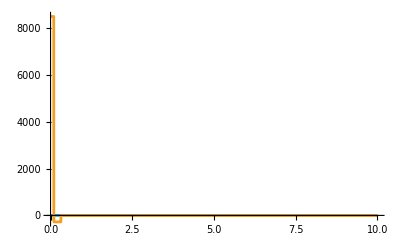

```mathematica
Plot[{ϕi[r, nrem],Evaluate[D[(D[(D[(ϕi[r, nrem]), r]), r]), r]]}, {r, 0, R}]
```

```mathematica
PiecewiseExpand[ϕi[r, nrem]]
```

Piecewise[{{1.46247529557426437022209928271474650374661723770280186965083387253251049318213758014936090093103337-13.874258867227931106662978481442395112398517131084056089525016175975314795464127404480827027931001 r+43.874258867227931106662978481442395112398517131084056089525016175975314795464127404480827027931001 r^2-46.2475295574264370222099282714746503746617237702801869650833872532510493182137580149360900931033366 r^3, 0.1≤r≤0.31622776601683793319988935444327185337195551393252168268575048527925944386392382213442481083793003}, {30. r-394.868329805051379959966806332981556011586654179756504805725145583777833159177146640327443251379009 r^2+1416.22776601683793319988935444327185337195551393252168268575048527925944386392382213442481083793003 r^3, 0≤r<0.1}, {0, True}}]

```mathematica
PiecewiseExpand[ϕi[r, nrem] Z/r D[(ϕi[r, nrem]), r]]
```

Piecewise[{{1.2034206511422260718238539478651188464509812783909286211451906405686224659003794452174407503×10^7 (0.0070610111169654240252262220320425959155679683429502551109391848173039689741988844852754521546-0.18587797776606915194954755593591480816886406331409948977812163036539206205160223102944909569 r+1. r^2) (0.0211830333508962720756786660961277877467039050288507653328175544519119069225966534558263564638-0.278816966649103727924321333903872212253296094971149234667182445548088093077403346544173643536 r+1. r^2), 0≤r<0.1}, {1/r 12833.003940990191602961323769529953383288229836037358262011118300433473242428501068658145346 (0.1-0.63245553203367586639977870888654370674391102786504336537150097055851888772784764426884962168 r+1. r^2) (-0.0316227766016837933199889354443271853371955513932521682685750485279259443863923822134424810838+0.3 r-0.948683298050513799599668063329815560115866541797565048057251455837778331591771466403274432514 r^2+1. r^3), 0.1<r≤0.31622776601683793319988935444327185337195551393252168268575048527925944386392382213442481083793003}, {-1/r 264652.17340356843053029824585931794886468211278564376352848920521907282266685404702095839521 (0.0056358931807149699672366277702054076446557455911345902796680837684717463085605069406031589334-0.17903019848460332665938591728226786836547905457580768672881512972632705473523566820902292421 r+1. r^2) (-0.0316227766016837933199889354443271853371955513932521682685750485279259443863923822134424810838+0.3 r-0.948683298050513799599668063329815560115866541797565048057251455837778331591771466403274432514 r^2+1. r^3), r==0.1}, {0, True}}]

```mathematica
1.2034206511422260718238539478651188464509812783909286211451906405686224659003794452174407503060676389647`92.76213006326844*^7 (0.0070610111169654240252262220320425959155679683429502551109391848173039689741988844852754521546132429773086961404028`92.77451717583303)
```

84973.66596101027599199336126659631120231733083595130096114502911675556663183542932806548865

## Test IPP Coefficient

### Matrix W

```mathematica
Evaluate[Table[(ϕi[R, ai] Z/R D[(ϕi[R, aj]), r]-Limit[ϕi[r, ai] Z/r D[(ϕi[r, aj]), r], r-> 0])+(ϕi[R, ai](Z k)/R^2 ϕi[R, aj]-Limit[ϕi[r, ai](Z k)/R^2 ϕi[r, aj], r-> 0]), {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(Indeterminate | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Series[ϕi[r, 1] Z/r D[(ϕi[r, 1]), r], {r, 0, 0}, Assumptions->Element[r, PositiveReals]]
```

1800.+O[r]^1

```mathematica
Evaluate[Table[ϕi[R, ai](Z k)/R^2 ϕi[R, aj]-Limit[ϕi[r, ai](Z k)/R^2 ϕi[r, aj], r-> 0], {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

### Matrix B plus

```mathematica
Evaluate[Table[ϕi[R, ai]D[(D[(ϕi[R, aj]), r]), r]-ϕi[0, ai]D[(D[(ϕi[0, aj]), r]), r], {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Evaluate[Table[ϕi[R, ai](k(1-k))/R^2 ϕi[R, aj]-Limit[ϕi[r, ai](k(1-k))/r^2 ϕi[r, aj], r-> 0], {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(Indeterminate | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Series[ϕi[r,1](k(1-k))/r^2 ϕi[r, 1], {r, 0, 0}, Assumptions->Element[r, PositiveReals]]
```

-1800.+O[r]^1

### Matrix B minus

```mathematica
Evaluate[Table[ϕi[R, ai](k(1-k))/R^2 ϕi[R, aj]-Limit[ϕi[r, ai](k(1+k))/r^2 ϕi[r, aj], r-> 0], {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

### Matrix A

```mathematica
Evaluate[Table[ϕi[R, ai] Z/R ϕi[R, aj]-Limit[ϕi[r, ai] Z/r ϕi[r, aj], r-> 0], {ai, nrem, n- nrem}, {aj, nrem, n- nrem}]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(6*^-4)/(4 c^2)
```

7.98770429535025732928483159441314074162678652254218244495610730917364950928045044719157555953842511×10^-9